## Write Data to files.

Preparing

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

Test Legend fuctioning.

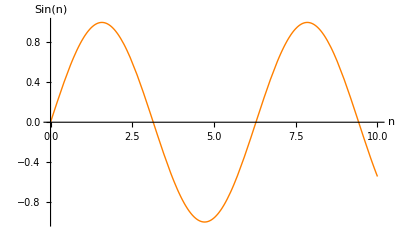

```mathematica
(*********************************************)
Print[Style["Preparing",30,Bold,Orange]]
(*********************************************)
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
(*********************************************)
(*Manually set the start point(a<1) of this table.*)
tranzs=31 ;tranzDE2=23;tranzDE3=23;tranzDE4=24;tranzDE5=24;tranzL=23;
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
norts=138-tranzs;nortL=138-tranzL;nort2=138-tranzDE2;nort3=138-tranzDE3;nort4=138-tranzDE4;nort5=138-tranzDE5;
nort=138-tranzL;
(**************************)
Print[Style["Test Legend fuctioning.",30,Bold,Orange]]
Plot[Sin[n],{n,0,10},PlotStyle->Orange,AxesLabel-> {"n","Sin(n)"},PlotLegend->{"Sin"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Parameters",30,Bold,Orange]]
(*********************************************)
w1 =-1;
w0 =-1;
wa=0.1;
w30=-1;
w3a=-0.1;
w3=w30+w2a (1-a);
w40=-0.92;
w4a=0.35;
w50=-0.9;
w5a=0.1;
ΩDE0 =0.73;
Ωk0=0;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
h=0.71;
(*h=1;*)
 (*H0 =(100 h)/300000;*)
H0=100 h;(*the real value is not very important here. this means all length units are MPc/h, all wavenumber units are h/MPc*)
Ωm0s =1; 
Ωr0s =8.09*10^-5;
(*Ωr0s=0;*)
nzs=nzL=nz2=nz3=nz4=nz5=aeq=Ωr0/Ωm0
c=300000
```

Parameters

0.00029963

300000

```mathematica
(*********************************************)
Print[Style["Intial conditions for Hubble constant, normalized at early time",30,Bold,Orange]]
(*********************************************)
HL0=H20=H30=H40=H50=H0;
Hs0=H0;
```

Intial conditions for Hubble constant, normalized at early time

```mathematica
(*********************************************)
Print[Style["Define Hubble functions",30,Bold,Orange]]
(*********************************************)
Hs[a_]:= Hs0  √(Ωr0s a^-4+Ωm0s a^-3);
HL[a_]:= HL0  √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w1)))
H2[a_]:= H20 √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w0+wa))Exp[-3 wa (1-a)])
H3[a_]:= H30 √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w30+w3a))Exp[-3 w3a (1-a)])
H4[a_]:= H40 √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w40+w4a))Exp[-3 w4a (1-a)])
H5[a_]:= H50 √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w50+w5a))Exp[-3 w5a (1-a)])
iHs[a_]:= Hs0  √(Ωm0s a^-1);
iHL[a_]:= HL0  √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w1)+2))
iH2[a_]:= H20 √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w0+wa))Exp[-3 wa (1-a)])
iH3[a_]:= H30 √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w30+w3a))Exp[-3 w3a (1-a)])
iH4[a_]:= H40 √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w40+w4a))Exp[-3 w4a (1-a)])
iH5[a_]:= H50 √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w50+w5a))Exp[-3 w5a (1-a)])
```

Define Hubble functions

```mathematica
(*********************************************)
Print[Style["Particle Horizon",30,Bold,Orange]]
(*********************************************)
dHs[a_?NumberQ]:=c a NIntegrate[1/(Hs[x] x^2),{x,0,a}];
dHL[a_?NumberQ]:=c a NIntegrate[1/(HL[x] x^2),{x,0,a}];
dH2[a_?NumberQ]:=c a NIntegrate[1/(H2[x] x^2),{x,0,a}];
dH3[a_?NumberQ]:=c a NIntegrate[1/(H3[x] x^2),{x,0,a}];
dH4[a_?NumberQ]:=c a NIntegrate[1/(H4[x] x^2),{x,0,a}];
dH5[a_?NumberQ]:=c a NIntegrate[1/(H5[x] x^2),{x,0,a}];
```

Particle Horizon

```mathematica
(*********************************************)
Print[Style["Define k of a",30,Bold,Orange]]
(*********************************************)
kL[a_]:= 1/dHL[a];ks[a_]:= 1/dHs[a];kDE2[a_]:= 1/dH2[a];kDE3[a_]:=1/dH3[a];kDE4[a_]:=1/dH4[a];kDE5[a_]:=1/dH5[a];
1/dHL[0.01]
{keqL=1/dHL[aeq],keq2=1/dH2[aeq],keq3=1/dH3[aeq],keq4=1/dH4[aeq],keq5=1/dH5[aeq]}
{k0L=1/dHL[1],k02=1/dH2[1],k03=1/dH3[1],k04=1/dH4[1],k05=1/dH5[1]}
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k== H2[a2],a2];*)
```

Define k of a

0.0730456

{28.6212,28.6212,28.6212,28.6212,28.6212}

{0.0000699507,0.0000701488,0.0000697716,0.0000715517,0.0000709509}

```mathematica
(*********************************************)
Print[Style["The equation for growth factors",30,Bold,Orange]]
(*********************************************)
```

The equation for growth factors

Define growth factors

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{DgL→InterpolatingFunction[{{0.001,10000.}},<>]}}

{{Dg2→InterpolatingFunction[{{0.001,10000.}},<>]}}

{{Dg3→InterpolatingFunction[{{0.001,10000.}},<>]}}

{{Dg4→InterpolatingFunction[{{0.001,10000.}},<>]}}

{{Dg5→InterpolatingFunction[{{0.001,10000.}},<>]}}

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.434321} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

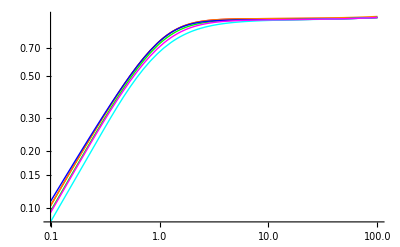

```mathematica
(*********************************************)
Print[Style["Define growth factors",30,Bold,Orange]]
(*********************************************)
Growths[a_]:= 5/2 Ωm0s  Hs[a]/Hs0 NIntegrate[1/(iHs[x]/Hs0)^3,{x,0,a}];
GrowthL[a_]:= 5/2 Ωm0  HL[a]/HL0 NIntegrate[1/(iHL[x]/HL0)^3,{x,0,a}];
solL=NDSolve[{a^2×D[DgL[a], a,a]+3/2×a×(1+HL[a]^-2×HL0^2×ΩDE0)×D[DgL[a], a]-3/2×HL[a]^-2×HL0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-3]==N[Growths[10^-3]],DgL'[10^-2]==N[Growths'[10^-2]]},DgL,{a,0.001,10000}]
GrowthL2[a_]:=DgL[a]/.solL[[1]]
sol2=NDSolve[{a^2×D[Dg2[a], a,a]+3/2×a×(1-(w0+wa (1-a))×H2[a]^-2×H20^2×ΩDE0×a^(-3×(1+(w0+wa (1-a)))))×D[Dg2[a], a]-3/2×H2[a]^-2×H20^2×Ωm0 a^-3×Dg2[a]==0,Dg2[10^-7]==N[GrowthL2[10^-7]],Dg2'[10^-7]==N[GrowthL2'[10^-7]]},Dg2,{a,0.001,10000}]
GrowthDE21[a_]:=Dg2[a]/.sol2[[1]]
sol3=NDSolve[{a^2×D[Dg3[a], a,a]+3/2×a×(1-(w30+w3a (1-a))×H3[a]^-2×H30^2×ΩDE0×a^(-3×(1+(w30+w3a (1-a)))))×D[Dg3[a], a]-3/2×H3[a]^-2×H30^2×Ωm0 a^-3×Dg3[a]==0,Dg3[10^-7]==N[GrowthL2[10^-7]],Dg3'[10^-7]==N[GrowthL2'[10^-7]]},Dg3,{a,0.001,10000}]
GrowthDE31[a_]:=Dg3[a]/.sol3[[1]]
sol4=NDSolve[{a^2×D[Dg4[a], a,a]+3/2×a×(1-(w40+w4a (1-a))×H4[a]^-2×H40^2×ΩDE0×a^(-3×(1+(w40+w4a (1-a)))))×D[Dg4[a], a]-3/2×H4[a]^-2×H40^2×Ωm0 a^-3×Dg4[a]==0,Dg4[10^-7]==N[GrowthL2[10^-7]],Dg4'[10^-7]==N[GrowthL2'[10^-7]]},Dg4,{a,0.001,10000}]
GrowthDE41[a_]:=Dg4[a]/.sol4[[1]]
sol5=NDSolve[{a^2×D[Dg5[a], a,a]+3/2×a×(1-(w50+w5a (1-a))×H5[a]^-2×H50^2×ΩDE0×a^(-3×(1+(w50+w5a (1-a)))))×D[Dg5[a], a]-3/2×H5[a]^-2×H50^2×Ωm0 a^-3×Dg5[a]==0,Dg5[10^-7]==N[GrowthL2[10^-7]],Dg5'[10^-7]==N[GrowthL2'[10^-7]]},Dg5,{a,0.001,10000}]
GrowthDE51[a_]:=Dg5[a]/.sol5[[1]]
GrowthDE2[a_]=GrowthL[1/101]/GrowthDE21[1/101] GrowthDE21[a];
GrowthDE3[a_]=GrowthL[1/101]/GrowthDE31[1/101] GrowthDE31[a];
GrowthDE4[a_]=GrowthL[1/101]/GrowthDE41[1/101] GrowthDE41[a];
GrowthDE5[a_]=GrowthL[1/101]/GrowthDE51[1/101] GrowthDE51[a];
LogLogPlot[{mn GrowthL[1/mn],mn GrowthL2[1/mn],mn GrowthDE2[1/mn],mn GrowthDE3[1/mn],mn GrowthDE4[1/mn],mn GrowthDE5[1/mn]},{mn,0.1,100},PlotStyle->{Red,Orange,Green,Blue,Cyan,Magenta},PlotLegend->{"LCDM_S", "LCDM_N","DE2","DE3","DE4","DE5"},LegendPosition->{1.1,-0.4}]
```

Plot k of a

0.000119402

0.0000699507

0.0000701488

0.0000697716

0.0000715517

0.0000709509

28.5557

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0000862641}. NIntegrate obtained -0.00024017 + 0.00912658\ ⅈ and 0.0000301288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.000327511}. NIntegrate obtained -0.000898138 + 0.0175416\ ⅈ and 0.0000957909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.000327511}. NIntegrate obtained -0.000903175 - 0.0175412\ ⅈ and 0.0000957909 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

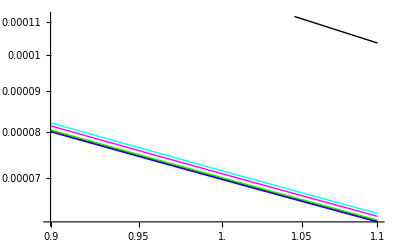

```mathematica
(*********************************************)
Print[Style["Plot k of a",30,Bold,Orange]]
(*********************************************)
ks[1]
kL[1]
kDE2[1]
kDE3[1]
kDE4[1]
kDE5[1]
kL[3*10^-4]
LogLogPlot[{ks[a],kL[a],kDE2[a],kDE3[a],kDE4[a],kDE5[a]},{a,0.9,1.1},PlotStyle->{Black,Red,Green,Blue,Cyan,Magenta}]
```

Plot growth factors of a for LCDM

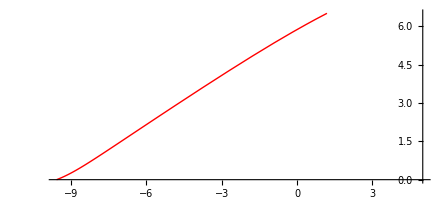

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for LCDM",30,Bold,Orange]]
(*********************************************)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {5,0},PlotStyle->{Red}]
```

Plot growth factors of a for all models

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained -46.4188 - 104.359\ ⅈ and 81.5626 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {-9.21015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

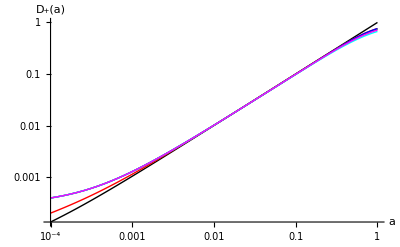

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for all models",30,Bold,Orange]]
(*********************************************)
LogLogPlot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a],GrowthDE4[a],GrowthDE5[a]},{a,10^-4,1},PlotStyle->{Black,Red,Green,Blue,Cyan,Magenta},AxesLabel-> {a,"D_+(a)"},PlotLegend->{"sCDM", "LCDM","DE2","DE3","DE4"},LegendPosition->{1.1,-0.4}]
```

Plot growth factors of a for all models

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained -46.4188 - 104.359\ ⅈ and 81.5626 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {-9.21015} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

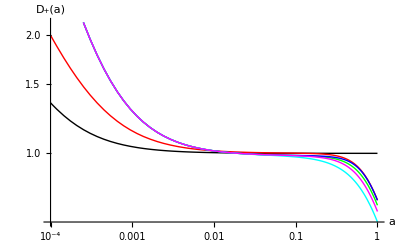

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for all models",30,Bold,Orange]]
(*********************************************)
LogLogPlot[{Growths[a]/a,GrowthL[a]/a,GrowthDE2[a]/a,GrowthDE3[a]/a,GrowthDE4[a]/a,GrowthDE5[a]/a},{a,10^-4,1},PlotStyle->{Black,Red,Green,Blue,Cyan,Magenta},AxesLabel-> {a,"D_+(a)"},PlotLegend->{"sCDM", "LCDM","DE2","DE3","DE4","DE5"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Tranform growth factors / Hubble distances of a to those of 1+z",30,Bold,Orange]]
(*********************************************)
GS[mn_]:=Growths[1/mn];GL[mn_]:=GrowthL[1/mn];GDE2[mn_]:=GrowthDE2[1/mn];GDE3[mn_]:=GrowthDE3[1/mn];GDE4[mn_]:=GrowthDE4[1/mn];GDE5[mn_]:=GrowthDE5[1/mn];
Lambdas[mn_]:=dHs[1/mn];LambdaL[mn_]:=dHL[1/mn];Lambda2[mn_]:=dH2[1/mn];Lambda3[mn_]:=dH3[1/mn];Lambda4[mn_]:=dH4[1/mn];Lambda5[mn_]:=dH5[1/mn];
```

Tranform growth factors / Hubble distances of a to those of 1+z

```mathematica
(*********************************************)
Print[Style["Plot Hubble distances",30,Bold,Orange]]
(*********************************************)
```

Plot Hubble distances

```mathematica
(*********************************************)
Print[Style["Plot growth factors in terms of 1+z",30,Bold,Orange]]
(*********************************************)
LogLogPlot[{mn GrowthL[1/mn],mn GrowthL2[1/mn],mn GrowthDE2[1/mn],mn GrowthDE3[1/mn],mn GrowthDE4[1/mn],mn GrowthDE5[1/mn]},{mn,0.1,100},PlotStyle->{Red,Orange,Green,Blue,Cyan,Magenta},PlotLegend->{"sCDM", "LCDM","DE2","DE3","DE4","DE5"},LegendPosition->{1.1,-0.4}]
```

Plot growth factors in terms of 1+z

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.434321} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-

Import power spectrum of LCDM calculated by cmbeasy, and some test

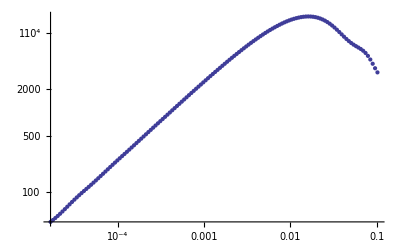

0.0000167287

0.000112794

281.02

138

0.0000118774==71. √(0.73+0.0000809/aL^4+0.27/aL^3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717717},{aL→-0.00029963}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717717},{aL→-0.00029963}}

```mathematica
(*********************************************)
Print[Style["Import power spectrum of LCDM calculated by cmbeasy, and some test",30,Bold,Orange]]
(*********************************************)
PowerS=Import["cdm_11-27_cut.dat"];
ListLogLogPlot[PowerS]
PowerS[[1,1]]
PowerS[[tranzs]][[1]]
PowerS[[tranzs]][[2]]
leth=Length[PowerS]
PowerS[[1,1]]h== HL[aL]
Solve[PowerS[[1,1]]h== HL[aL],aL,Reals]
NSolve[PowerS[[1,1]]h== HL[aL],aL,Reals]
```

```mathematica
(*********************************************)
Print[Style["Tests for Hubble equations",30,Bold,Orange]]
(*********************************************)
HL[1]/h
HL[0.01]/h
HL[0.001]/h
HL[0.0001]/h
HL[0.00001]/h
HL[0.000001]/h
```

Tests for Hubble equations

100.004

52734.3

1.87323×10^6

1.03875×10^8

9.1433×10^9

9.00944×10^11

```mathematica
aokTabs11=Table[as/.FindRoot[PowerS[[i,1]]==ks[as],{as,0.0001}],{i,1,leth}];
aokTabL11=Table[aL/.FindRoot[PowerS[[i,1]]==kL[aL],{aL,0.0001}],{i,1,leth}];
aokTabDE211=Table[a2/.FindRoot[PowerS[[i,1]]==kDE2[a2],{a2,0.0001}],{i,1,leth}];
aokTabDE311=Table[a3/.FindRoot[PowerS[[i,1]]==kDE3[a3],{a3,0.0001}],{i,1,leth}];
aokTabDE411=Table[a4/.FindRoot[PowerS[[i,1]]==kDE4[a4],{a4,0.0001}],{i,1,leth}];
aokTabDE511=Table[a5/.FindRoot[PowerS[[i,1]]==kDE5[a5],{a5,0.0001}],{i,1,leth}];
Export["CPL\\CPL_Sync_2012-02-19\\aokTabs11.xls",aokTabs11,"XLS"]
Export["CPL\\CPL_Sync_2012-02-19\\aokTabL11.xls",aokTabL11,"XLS"]
Export["CPL\\CPL_Sync_2012-02-19\\aokTabDE211.xls",aokTabDE211,"XLS"]
Export["CPL\\CPL_Sync_2012-02-19\\aokTabDE311.xls",aokTabDE311,"XLS"]
Export["CPL\\CPL_Sync_2012-02-19\\aokTabDE411.xls",aokTabDE411,"XLS"]
Export["CPL\\CPL_Sync_2012-02-19\\aokTabDE511.xls",aokTabDE511,"XLS"]
```

CPL\CPL_Sync_2012-02-19\aokTabs11.xls

CPL\CPL_Sync_2012-02-19\aokTabL11.xls

CPL\CPL_Sync_2012-02-19\aokTabDE211.xls

CPL\CPL_Sync_2012-02-19\aokTabDE311.xls

CPL\CPL_Sync_2012-02-19\aokTabDE411.xls

CPL\CPL_Sync_2012-02-19\aokTabDE511.xls

```mathematica
(*********************************************)
Print[Style["Create tables for power spectrums, and test",30,Bold,Orange]]
(*********************************************)
(*Manually set the start point(a≤1) of this table.*)(*Moved to the beginning of the file.*)
(*tranzs=43;tranzL=43;tranzDE2=43;tranzDE3=43;tranzDE4=43;*)
(********)
aokTabs=Table[as/.FindRoot[PowerS[[i,1]]==ks[as],{as,0.0001}],{i,tranzs+1,leth}];
aokTabL=Table[aL/.FindRoot[PowerS[[i,1]]==kL[aL],{aL,0.0001}],{i,tranzL+1,leth}];
aokTabDE2=Table[a2/.FindRoot[PowerS[[i,1]]==kDE2[a2],{a2,0.0001}],{i,tranzDE2+1,leth}];
aokTabDE3=Table[a3/.FindRoot[PowerS[[i,1]]==kDE3[a3],{a3,0.0001}],{i,tranzDE3+1,leth}];
aokTabDE4=Table[a4/.FindRoot[PowerS[[i,1]]==kDE4[a4],{a4,0.0001}],{i,tranzDE4+1,leth}];
aokTabDE5=Table[a5/.FindRoot[PowerS[[i,1]]==kDE5[a5],{a5,0.0001}],{i,tranzDE5+1,leth}];
(*Check the results*)
aokTabs[[1]]
Length[aokTabL]
Length[aokTabs]
Length[aokTabDE2]
Length[aokTabDE3]
Length[aokTabDE4]
Length[aokTabDE5]
aokTabs
aokTabL
aokTabDE2
aokTabDE3
aokTabDE4
aokTabDE5
```

Create tables for power spectrums, and test

0.995573

115

107

115

115

114

114

{0.995573,0.954356,0.914848,0.876979,0.840679,0.805884,0.772532,0.740562,0.709917,0.680543,0.652386,0.625396,0.599525,0.574726,0.550954,0.528168,0.506326,0.485389,0.46532,0.446082,0.427642,0.409965,0.39302,0.376778,0.361208,0.346283,0.331977,0.318263,0.305117,0.292515,0.280435,0.268856,0.257755,0.247115,0.236915,0.227137,0.217764,0.208779,0.200166,0.191909,0.183994,0.176406,0.169133,0.16216,0.155476,0.149068,0.142926,0.137037,0.131392,0.125981,0.120793,0.11582,0.111052,0.106482,0.1021,0.0978995,0.0938726,0.0900121,0.0863111,0.082763,0.0793615,0.0761005,0.0729742,0.069977,0.0671035,0.0643487,0.0617076,0.0591756,0.056748,0.0544206,0.0521893,0.05005,0.0479989,0.0460324,0.0441471,0.0423395,0.0406064,0.0389447,0.0373515,0.035824,0.0343594,0.0329551,0.0316087,0.0303177,0.0290799,0.027893,0.026755,0.0256638,0.0246175,0.0236143,0.0226523,0.0217298,0.0208453,0.0199971,0.0191838,0.0184039,0.017656,0.0169389,0.0162512,0.0155917,0.0149592,0.0143528,0.0137711,0.0132134,0.0126785,0.0121655,0.0116735}

{0.975311,0.929032,0.885366,0.844138,0.805184,0.76835,0.733496,0.700488,0.669206,0.639534,0.61137,0.584615,0.559182,0.534987,0.511955,0.490017,0.469109,0.449169,0.430145,0.411986,0.394644,0.378076,0.362241,0.347103,0.332627,0.318779,0.305529,0.292848,0.28071,0.269089,0.257962,0.247306,0.237099,0.227322,0.217956,0.208982,0.200383,0.192144,0.184248,0.176681,0.169429,0.162477,0.155815,0.149428,0.143306,0.137438,0.131812,0.126419,0.121249,0.116292,0.11154,0.106984,0.102616,0.0984279,0.0944124,0.0905623,0.0868708,0.0833312,0.0799373,0.076683,0.0735626,0.0705705,0.0677013,0.06495,0.0623118,0.0597819,0.0573559,0.0550294,0.0527984,0.050659,0.0486072,0.0466396,0.0447526,0.042943,0.0412074,0.0395429,0.0379466,0.0364156,0.0349472,0.0335389,0.0321881,0.0308926,0.02965,0.0284581,0.0273149,0.0262184,0.0251665,0.0241576,0.0231898,0.0222615,0.0213709,0.0205167,0.0196972,0.018911,0.0181568,0.0174333,0.0167391,0.0160732,0.0154343,0.0148213,0.0142331,0.0136688,0.0131274,0.0126079,0.0121094,0.0116311,0.0111721,0.0107316,0.010309,0.00990339,0.00951415,0.0091406,0.0087821,0.00843803,0.00810781}

{0.977446,0.931075,0.88732,0.846003,0.806961,0.770038,0.735094,0.701996,0.670623,0.640861,0.612607,0.585765,0.560246,0.535969,0.512858,0.490844,0.469863,0.449857,0.430769,0.412551,0.395154,0.378535,0.362655,0.347474,0.332959,0.319075,0.305793,0.293084,0.28092,0.269276,0.258127,0.247452,0.237229,0.227437,0.218057,0.209071,0.200462,0.192213,0.184309,0.176734,0.169475,0.162519,0.155851,0.14946,0.143334,0.137462,0.131834,0.126438,0.121265,0.116306,0.111553,0.106995,0.102625,0.0984361,0.0944196,0.0905686,0.0868762,0.083336,0.0799415,0.0766866,0.0735657,0.0705732,0.0677037,0.0649521,0.0623136,0.0597835,0.0573572,0.0550306,0.0527995,0.0506599,0.048608,0.0466403,0.0447532,0.0429435,0.0412079,0.0395433,0.0379469,0.0364159,0.0349475,0.0335391,0.0321883,0.0308928,0.0296501,0.0284582,0.027315,0.0262185,0.0251666,0.0241577,0.0231899,0.0222615,0.021371,0.0205167,0.0196972,0.018911,0.0181568,0.0174333,0.0167391,0.0160732,0.0154343,0.0148213,0.0142331,0.0136688,0.0131274,0.0126079,0.0121094,0.0116311,0.0111721,0.0107316,0.010309,0.00990339,0.00951415,0.0091406,0.0087821,0.00843803,0.00810781}

{0.973378,0.927183,0.883599,0.842452,0.803579,0.766829,0.732059,0.699136,0.667939,0.638352,0.610272,0.583599,0.558246,0.534129,0.511171,0.489303,0.468461,0.448584,0.429617,0.411511,0.394218,0.377695,0.361902,0.346802,0.332359,0.318541,0.305319,0.292663,0.280547,0.268946,0.257836,0.247195,0.237002,0.227237,0.217882,0.208917,0.200327,0.192095,0.184205,0.176644,0.169396,0.162449,0.15579,0.149407,0.143288,0.137422,0.131799,0.126407,0.121239,0.116283,0.111533,0.106978,0.10261,0.098423,0.0944082,0.0905587,0.0868677,0.0833285,0.079935,0.076681,0.0735609,0.070569,0.0677,0.064949,0.0623109,0.0597811,0.0573552,0.0550288,0.0527979,0.0506585,0.0486069,0.0466393,0.0447523,0.0429427,0.0412072,0.0395428,0.0379465,0.0364155,0.0349471,0.0335388,0.0321881,0.0308925,0.0296499,0.0284581,0.0273149,0.0262183,0.0251665,0.0241576,0.0231898,0.0222615,0.0213709,0.0205167,0.0196972,0.018911,0.0181568,0.0174333,0.0167391,0.0160732,0.0154342,0.0148213,0.0142331,0.0136688,0.0131274,0.0126079,0.0121094,0.0116311,0.0111721,0.0107316,0.010309,0.00990338,0.00951415,0.0091406,0.0087821,0.00843803,0.00810781}

{0.945437,0.901009,0.859018,0.819301,0.781708,0.746098,0.712344,0.680327,0.649938,0.621074,0.593644,0.56756,0.542743,0.519118,0.496618,0.475178,0.454739,0.435247,0.416651,0.398902,0.381957,0.365775,0.350315,0.335543,0.321423,0.307924,0.295016,0.28267,0.27086,0.259561,0.248748,0.238399,0.228493,0.21901,0.209931,0.201237,0.192911,0.184938,0.1773,0.169985,0.162977,0.156263,0.14983,0.143667,0.137761,0.132102,0.126679,0.121482,0.116501,0.111727,0.107152,0.102766,0.0985622,0.0945326,0.09067,0.0869672,0.0834175,0.0800145,0.0767522,0.0736245,0.0706258,0.0677509,0.0649944,0.0623515,0.0598174,0.0573877,0.0550579,0.0528239,0.0506817,0.0486276,0.0466578,0.0447689,0.0429576,0.0412205,0.0395546,0.0379571,0.036425,0.0349556,0.0335464,0.0321949,0.0308986,0.0296554,0.0284629,0.0273192,0.0262222,0.02517,0.0241607,0.0231926,0.022264,0.0213732,0.0205187,0.0196989,0.0189126,0.0181582,0.0174345,0.0167403,0.0160742,0.0154352,0.0148221,0.0142339,0.0136695,0.013128,0.0126084,0.0121099,0.0116315,0.0111725,0.010732,0.0103093,0.00990366,0.00951439,0.00914082,0.0087823,0.00843821,0.00810797}

{0.939277,0.89509,0.853327,0.813831,0.776454,0.74106,0.707521,0.67572,0.645548,0.616901,0.589687,0.563818,0.539213,0.515796,0.4935,0.472258,0.452011,0.432704,0.414285,0.396705,0.379922,0.363891,0.348576,0.333939,0.319947,0.306567,0.29377,0.281528,0.269814,0.258604,0.247873,0.237601,0.227765,0.218347,0.209327,0.200687,0.192412,0.184484,0.176888,0.169611,0.162638,0.155956,0.149552,0.143415,0.137533,0.131896,0.126493,0.121313,0.116349,0.11159,0.107027,0.102654,0.0984611,0.0944415,0.0905878,0.0868931,0.0833507,0.0799544,0.076698,0.0735756,0.0705819,0.0677113,0.0649588,0.0623194,0.0597886,0.0573617,0.0550345,0.0528029,0.0506629,0.0486106,0.0466426,0.0447552,0.0429452,0.0412094,0.0395447,0.0379481,0.0364169,0.0349484,0.0335399,0.032189,0.0308934,0.0296507,0.0284587,0.0273154,0.0262188,0.0251669,0.024158,0.0231901,0.0222617,0.0213712,0.0205169,0.0196973,0.0189111,0.0181569,0.0174334,0.0167392,0.0160733,0.0154343,0.0148213,0.0142332,0.0136689,0.0131274,0.0126079,0.0121094,0.0116311,0.0111721,0.0107317,0.010309,0.0099034,0.00951416,0.00914061,0.00878211,0.00843804,0.00810782}

```mathematica
(*********************************************)
Print[Style["Export aok table",30,Bold,Orange]]
(*********************************************)
Export["CPL\\CPL_Sync_2012-02-19\\aokTabs.xls",aokTabs,"XLS"]
Export["CPL\\CPL_Sync_2012-02-19\\aokTabL.xls",aokTabL,"XLS"]
Export["CPL\\CPL_Sync_2012-02-19\\aokTabDE2.xls",aokTabDE2,"XLS"]
Export["CPL\\CPL_Sync_2012-02-19\\aokTabDE3.xls",aokTabDE3,"XLS"]
Export["CPL\\CPL_Sync_2012-02-19\\aokTabDE4.xls",aokTabDE4,"XLS"]
Export["CPL\\CPL_Sync_2012-02-19\\aokTabDE5.xls",aokTabDE5,"XLS"]
```

Export aok table

CPL\CPL_Sync_2012-02-19\aokTabs.xls

CPL\CPL_Sync_2012-02-19\aokTabL.xls

CPL\CPL_Sync_2012-02-19\aokTabDE2.xls

CPL\CPL_Sync_2012-02-19\aokTabDE3.xls

CPL\CPL_Sync_2012-02-19\aokTabDE4.xls

CPL\CPL_Sync_2012-02-19\aokTabDE5.xls

```mathematica
(*********************************************)
Print[Style["Normalization factors. normalized to a early time of about a=10^-3",30,Bold,Orange]]
(*********************************************)
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
(*nort=197-tranzL*)
fracs=1/((Growths[1]/Growths[aokTabs[[norts]]])/(GrowthL[1]/GrowthL[aokTabL[[norts]]]))
frac2=1/((GrowthDE2[1]/GrowthDE2[aokTabDE2[[nort2]]])/(GrowthL[1]/GrowthL[aokTabL[[nort2]]]))
frac3=1/((GrowthDE3[1]/GrowthDE3[aokTabDE3[[nort3]]])/(GrowthL[1]/GrowthL[aokTabL[[nort3]]]))
frac4=1/((GrowthDE4[1]/GrowthDE4[aokTabDE4[[nort4]]])/(GrowthL[1]/GrowthL[aokTabL[[nort4]]]))
frac5=1/((GrowthDE5[1]/GrowthDE5[aokTabDE5[[nort5]]])/(GrowthL[1]/GrowthL[aokTabL[[nort5]]]))
```

Normalization factors. normalized to a early time of about a=10^-3

0.786394

1.03395

1.00415

1.0968

1.03109

```mathematica
(*********************************************)
Print[Style["Tables for Q factors",30,Bold,Orange]]
(*********************************************)
Qfactor2=Table[{PowerS[[i+tranzDE2,1]],frac2 (GrowthDE2[1]/GrowthDE2[aokTabDE2[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth-tranzDE2}];
Qfactor2Ex=Table[{PowerS[[i,1]],frac2(GrowthDE2[1]/GrowthDE2[aokTabDE2[[1]]])/(GrowthL[1]/GrowthL[aokTabL[[1]]])},{i,1,tranzDE2}];
Qfac2=Join[Qfactor2Ex,Qfactor2];
Qfactor2[[1]]
Qfactor2[[1]][[1]]
Export["CPL\\CPL_Sync_2012-02-19\\QfactorDE2vsL.xls",Qfac2,"XLS"]
Qfactor3=Table[{PowerS[[i+tranzDE3,1]],frac3 (GrowthDE3[1]/GrowthDE3[aokTabDE3[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth-tranzDE3}];
Qfactor3Ex=Table[{PowerS[[i,1]],frac3(GrowthDE3[1]/GrowthDE3[aokTabDE3[[1]]])/(GrowthL[1]/GrowthL[aokTabL[[1]]])},{i,1,tranzDE3}];
Qfac3=Join[Qfactor3Ex,Qfactor3];
Qfactor3[[1]]
Qfactor3[[1]][[1]]
Export["CPL\\CPL_Sync_2012-02-19\\QfactorDE3vsL.xls",Qfac3,"XLS"]
Qfactor4=Table[{PowerS[[i+tranzDE4,1]],frac4 (GrowthDE4[1]/GrowthDE4[aokTabDE4[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth-tranzDE4}];
Qfactor4Ex=Table[{PowerS[[i,1]],frac4(GrowthDE4[1]/GrowthDE4[aokTabDE4[[1]]])/(GrowthL[1]/GrowthL[aokTabL[[1]]])},{i,1,tranzDE4}];
Qfac4=Join[Qfactor4Ex,Qfactor4];
Qfactor4[[1]]
Qfactor4[[1]][[1]]
Export["CPL\\CPL_Sync_2012-02-19\\QfactorDE4vsL.xls",Qfac4,"XLS"]
Qfactor5=Table[{PowerS[[i+tranzDE5,1]],frac5 (GrowthDE5[1]/GrowthDE5[aokTabDE5[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth-tranzDE5}];
Qfactor5Ex=Table[{PowerS[[i,1]],frac5(GrowthDE5[1]/GrowthDE5[aokTabDE5[[1]]])/(GrowthL[1]/GrowthL[aokTabL[[1]]])},{i,1,tranzDE5}];
Qfac5=Join[Qfactor5Ex,Qfactor5];
Qfactor5[[1]]
Qfactor5[[1]][[1]]
Export["CPL\\CPL_Sync_2012-02-19\\QfactorDE5vsL.xls",Qfac5,"XLS"]
(*********************************************)
Print[Style["Q factors Exported!",30,Bold,Orange]]
(*********************************************)
```

Tables for Q factors

{0.0000722593,1.03276}

0.0000722593

CPL\CPL_Sync_2012-02-19\QfactorDE2vsL.xls

{0.0000722593,1.00522}

0.0000722593

CPL\CPL_Sync_2012-02-19\QfactorDE3vsL.xls

{0.0000770053,1.11334}

0.0000770053

CPL\CPL_Sync_2012-02-19\QfactorDE4vsL.xls

{0.0000770053,1.05058}

0.0000770053

CPL\CPL_Sync_2012-02-19\QfactorDE5vsL.xls

Q factors Exported!

```mathematica
(GrowthDE3[1]/GrowthDE2[1/aokTabDE3[[1]]])/(GrowthL[1]/GrowthL[1/aokTabL[[1]]])
Qfactor3[[1]]
Qfactor3Ex[[tranzDE3]]
frac3
frac2
PowerSS[[1,1]]
```

1.02879

{0.0000722593,1.00522}

{0.0000678057,1.00522}

1.00415

1.03395

Part::partd: Part specification PowerSS ⟦ 1, 1 ⟧ is longer than depth of object.

PowerSS⟦1,1⟧

```mathematica
(*********************************************)
Print[Style["Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.",30,Bold,Orange]]
(*********************************************)

(*********************************************)
Print[Style["Construct the normalized power spectrum (different units) and export them",30,Bold,Orange]]
(*********************************************)
PowerSS=Table[{PowerS[[i,1]],PowerS[[i,2]]},{i,1,leth}];
Export["CPL\\CPL_Sync_2012-02-19\\PowerSScale.xls",PowerSS,"XLS"]
PowerSDE2=Table[{PowerSS[[i,1]],(Qfac2[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
Export["CPL\\CPL_Sync_2012-02-19\\PowerSDE2.xls",PowerSDE2,"XLS"]
PowerSDE3=Table[{PowerSS[[i,1]],(Qfac3[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
Export["CPL\\CPL_Sync_2012-02-19\\PowerSDE3.xls",PowerSDE3,"XLS"]
PowerSDE4=Table[{PowerSS[[i,1]],(Qfac4[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
Export["CPL\\CPL_Sync_2012-02-19\\PowerSDE4.xls",PowerSDE4,"XLS"]
PowerSDE5=Table[{PowerSS[[i,1]],(Qfac5[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
Export["CPL\\CPL_Sync_2012-02-19\\PowerSDE5.xls",PowerSDE5,"XLS"]
ListLogLogPlot[PowerS]
ListLogLogPlot[PowerSS]
(*********************************************)
Print[Style["Export power spectrum raw data",30,Bold,Orange]]
(*********************************************)
```

Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.

Construct the normalized power spectrum (different units) and export them

CPL\CPL_Sync_2012-02-19\PowerSScale.xls

CPL\CPL_Sync_2012-02-19\PowerSDE2.xls

CPL\CPL_Sync_2012-02-19\PowerSDE3.xls

CPL\CPL_Sync_2012-02-19\PowerSDE4.xls

CPL\CPL_Sync_2012-02-19\PowerSDE5.xls

-Graphics-

-Graphics-

Export power spectrum raw data

Import the Q factors calculated previously.

Plot P(k)

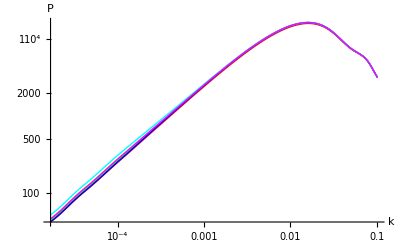

Plot Qfactors vs k

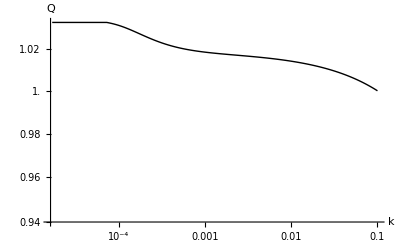

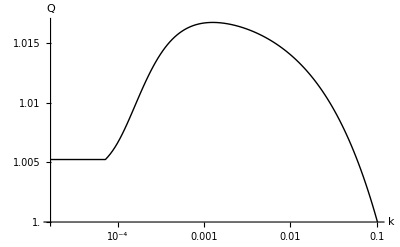

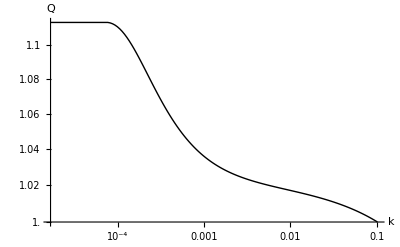

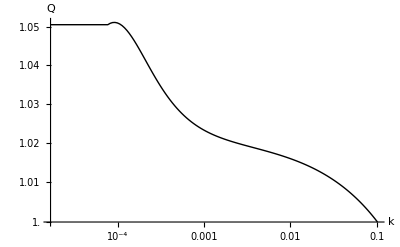

```mathematica
(*********************************************)
Print[Style["Import the Q factors calculated previously.",30,Bold,Orange]]
(*********************************************)
QfDe2VsL=Import["CPL\\CPL_Sync_2012-02-19\\QfactorDE2vsL.xls"];
QfDe3VsL=Import["CPL\\CPL_Sync_2012-02-19\\QfactorDE3vsL.xls"];
QfDe4VsL=Import["CPL\\CPL_Sync_2012-02-19\\QfactorDE4vsL.xls"];
QfDe5VsL=Import["CPL\\CPL_Sync_2012-02-19\\QfactorDE5vsL.xls"];
(*********************************************)
Print[Style["Plot P(k)",30,Bold,Orange]]
(*********************************************)
ListLogLogPlot[{PowerSS,PowerSDE2,PowerSDE3,PowerSDE4,PowerSDE5},Joined->True,AxesLabel->{k,P},PlotRange->Automatic,PlotStyle->{Red,Green,Blue,Cyan,Magenta},PlotLegend->{"LCDM","w2","w3","w4","w5"},LegendPosition->{1.1,-0.4}]
(*********************************************)
Print[Style["Plot Qfactors vs k",30,Bold,Orange]]
(*********************************************)
ListLogLogPlot[{QfDe2VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Automatic,PlotStyle->{Black},AxesOrigin->{0.000016,0.94},PlotLegend->{"w2"},LegendPosition->{1.1,-0.4}]
ListLogLogPlot[{QfDe3VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Black},PlotLegend->{"w3"},LegendPosition->{1.1,-0.4}]
ListLogLogPlot[{QfDe4VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Black},PlotLegend->{"w4"},LegendPosition->{1.1,-0.4}]
ListLogLogPlot[{QfDe5VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Black},PlotLegend->{"w5"},LegendPosition->{1.1,-0.4}]
```

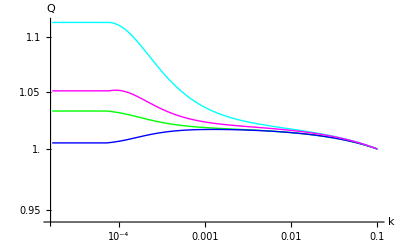

```mathematica
ListLogLogPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL,QfDe5VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Automatic,PlotStyle->{Green,Blue,Cyan,Magenta},AxesOrigin->{0.000016,0.94},PlotLegend->{"w2","w3","w4","w5"},LegendPosition->{1.1,-0.4}]
```

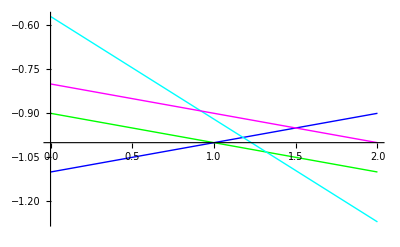

```mathematica
Plot[{-1+0.1(1-t),-1-0.1(1-t),-0.92+0.35(1-t),-0.9+0.1(1-t)},{t,0,2},AxesOrigin->{0,-1},PlotStyle->{Green,Blue,Cyan,Magenta,Red},PlotLegend->{"w2","w3","w4","w5"},LegendPosition->{1.1,-0.4}]
```